```mathematica
SeriesCoefficient[F[z]/.First[DSolve[{λ (r (z-1)^2-1/2 Δ (z^2-1)) F'[z]+λ Δ (z-1)==0,F[1]==1},F,z]],{z,0,m}];
p1[r_,Δ_,m_]:=Evaluate[FullSimplify[%,Assumptions->{r>0,r<1/2,Δ>0,m≥0,m∈Integers}]]
```

```mathematica
SeriesCoefficient[F[z,t]/.First[DSolve[{λ (r (z-1)^2-1/2 Δ (z^2-1)) D[F[z,t], z]==D[F[z,t], t],F[z,0]==z},F,{z,t}]],{z,0,m}];
p2[λ_,r_,Δ_,t_,m_]:=Evaluate[FullSimplify[%,Assumptions->{r>0,r<1/2,Δ>0,m≥0,m∈Integers,λ>0,t≥0}]]
```

((-0.49+0.51 ⅇ^(0.0077 t)) (1/(-1.+ⅇ^(0.0077 t))0.00077551 ⅇ^(0.0077 t) (-0.49+0.49 ⅇ^(0.0077 t))^m (-0.49+0.51 ⅇ^(0.0077 t))^(-1-m)+(0.00204082 0.960784^m)/m))/(0.0157613+0.00337087 ⅇ^(0.0077 t))

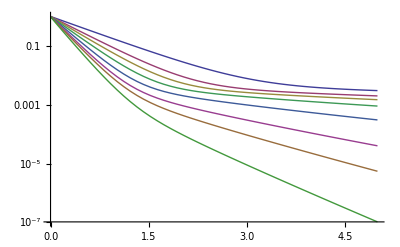

```mathematica
0.05 p1[0.25,0.01,m]+0.95 p2[0.77,0.25,0.01,t,m];
FullSimplify[%/(1-%/.m->0),Assumptions->{m≥1,m∈Integers,t≥0}]
1-∑_(m=1)^(n t) %;
LogPlot[Evaluate[Table[Tooltip[%,t],{t,{1,2,3,5,10,20,30,50}}]],{n,0,5}]
```